```mathematica
keVPerg=6.2415064799632 10^8;
keVPeV=10^-3;
```

```mathematica
griddir="D:\\Files\\Research\\Thesis\\test_run\\simgrid.h5";
x1=Import[griddir,"/x1"][[3;;-3]];
x2=Import[griddir,"/x2"][[3;;-3]];
x3=Import[griddir,"/x3"][[3;;-3]];
ar=Subtract@@@MinMax[x3]/Subtract@@@MinMax[x2];
mlat=90-(180/Pi)Import[griddir,"/theta"][[;;,1,-1]];
mlon=(180/Pi)Import[griddir,"/phi"][[1,;;,-1]];
```

```mathematica
contour[x_,span_,slope_]:=(span/2) Tanh[2slope x/span]
(*contour[x_,span_,slope_]:=(span /2)Sin[2π x/slope]*)
sheet[y_,pos_,wdth_,gsl_]:=(Tanh[2(y-pos+wdth/2)/(gsl wdth)]-Tanh[2(y-pos-wdth/2)/(gsl wdth)])/2
bar[x_,pos_,frac_,gsl_]:=(2-frac(1-Tanh[2(x-pos)/gsl]))/2
dim[t_,frc_,del_,tim_]:=(2-frc(1-Tanh[2(t-del)/tim]))/2
```

```mathematica
ctrSlope=1/2;
ctrSpan=100000;(*m*)
ctr[x_]:=contour[x,ctrSpan,ctrSlope]
dydxTemp=D[contour[xx,ctrSpan,ctrSlope],xx];
dydx[x_]:=dydxTemp/.xx->x
s[x_]:=1+0Sqrt[1+dydx[x]^2]
s[x_]:=1
```

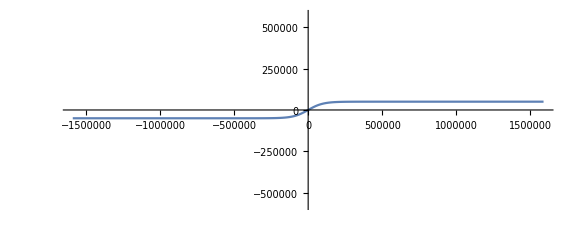

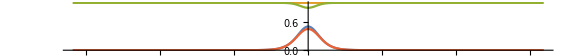

```mathematica
Plot[ctr[x],{x,Min[x2],Max[x2]},PlotRange->MinMax/@{x2,x3},ImageSize->Large,AspectRatio->ar]
Plot[{dydx[x],s[x],1/Sqrt[1+dydx[x]^2],dydx[x]/Sqrt[1+dydx[x]^2]},{x,Min[x2],Max[x2]},PlotRange->All,ImageSize->Large,AspectRatio->1/10]
```

```mathematica
KAmp=0.3;(*A m^-1*)
JWdth=400000;(*m*)
JGSL=0.1;(*%*)
J[x_,y_]:=(KAmp/JWdth) (sheet[y,ctr[x]+JWdth /2,JWdth s[x],JGSL]-sheet[y,ctr[x]-JWdth /2,JWdth s[x],JGSL])
DensityPlot[
J[x,y]
,{x,Min[x2],Max[x2]}
,{y,Min[x3],Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,PlotPoints->100
,ImageSize->Large
,AspectRatio->ar
]
```

-Graphics-

```mathematica
FAmp=2000;(*m s^-1*)
FWdth=50000;(*m*)
FGSL=0.3;(*%*)
F[x_,y_]:=FAmp (sheet[y,ctr[x]-JWdth,FWdth s[x],FGSL]-sheet[y,ctr[x],FWdth s[x],FGSL]+sheet[y,ctr[x]+JWdth,FWdth,FGSL])
U[x_,y_]:=F[x,y](1/Sqrt[1+dydx[x]^2])
V[x_,y_]:=F[x,y](dydx[x]/Sqrt[1+dydx[x]^2])
DensityPlot[
F[x,y]
,{x,Min[x2],Max[x2]}
,{y,Min[x3],Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,PlotPoints->100
,ImageSize->Large
,AspectRatio->ar
]
```

-Graphics-

```mathematica
zoom=0.2;
VectorPlot[
{U[x,y],V[x,y]}
,{x,zoom Min[x2],zoom Max[x2]}
,{y,zoom Min[x3],zoom Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,ImageSize->Large
,AspectRatio->ar
,VectorScale->0.03
,VectorPoints->25
]
```

-Graphics-

```mathematica
div=D[U[x,y],x]+D[V[x,y],y];
DensityPlot[
div
,{x,Min[x2],Max[x2]}
,{y,Min[x3],Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,PlotPoints->100
,ImageSize->Large
,AspectRatio->ar
]
```

-Graphics-

```mathematica
E0AmpH=10000;(*eV*)
E0AmpL=3000;(*eV*)
E0WdthH=20000;(*m*)
E0WdthL=200000;(*m*)
E0OffsetH=-0.6;(*%*)
E0OffsetL=100000;(*m*)
E0GSLH=0.4;(*%*)
E0GSLL=0.01;(*%*)
BarFrac=0;(*%*)
BarGSL=100000;(*m*)
BarSpeed=-3000;(*m s^-1*)
BarStart=-150 BarSpeed;(*m*)
DimFrc=1;
DimDel=100;
DimTim=100;
E0[x_,y_,t_]:=bar[x,BarStart+BarSpeed t,BarFrac,BarGSL]dim[t,DimFrc,DimDel,DimTim](E0AmpH -E0AmpL)sheet[y,ctr[x]+E0WdthL/2+E0OffsetL+E0OffsetH E0WdthL/2,E0WdthH s[x],E0GSLH]+E0AmpL sheet[y,ctr[x]+E0WdthL/2+E0OffsetL,E0WdthL s[x],E0GSLL]
DensityPlot[
E0[x,y,300]
,{x,Min[x2],Max[x2]}

,{y,Min[x3],Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,PlotPoints->100
,ImageSize->Large
,AspectRatio->ar
]
```

-Graphics-

```mathematica
Manipulate[
DensityPlot[
E0[x,y,t]
,{x,Min[x2],Max[x2]}
,{y,Min[x3],Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,PlotPoints->100
,ImageSize->Large
,AspectRatio->ar
]
,{t,0,300}]
```

```mathematica
QAmpH=15;(*mW m^-2 or erg s^-1 cm^-2*)(*ISSI 2002, section 4.1.1, figure 4.3, typical inverted-v example*)
QAmpL=3;(*mW m^-2 or erg s^-1 cm^-2*)
QWdthH=E0WdthH;(*m*)
QWdthL=0.9E0WdthL(*180000*);(*m*)
QOffsetH=E0OffsetH;(*%*)
QOffsetL=E0OffsetL;(*m*)
QGSLH=E0GSLH;(*%*)
QGSLL=E0GSLL;(*%*)
Q[x_,y_,t_]:=bar[x,BarStart+BarSpeed t,BarFrac,BarGSL](QAmpH -QAmpL)sheet[y,ctr[x]+E0WdthL/2+E0OffsetL+E0OffsetH E0WdthL/2,QWdthH s[x],QGSLH]+QAmpL sheet[y,ctr[x]+E0WdthL/2+E0OffsetL,QWdthL s[x],QGSLL]
(*Q[x_,y_]:=QAmp*)
DensityPlot[
Q[x,y,0]
,{x,Min[x2],Max[x2]}
,{y,Min[x3],Max[x3]}
,PlotRange->All
,ColorFunction->"TemperatureMap"
,PlotLegends->Automatic
,PlotPoints->100
,ImageSize->Large
,AspectRatio->ar
]
```

-Graphics-

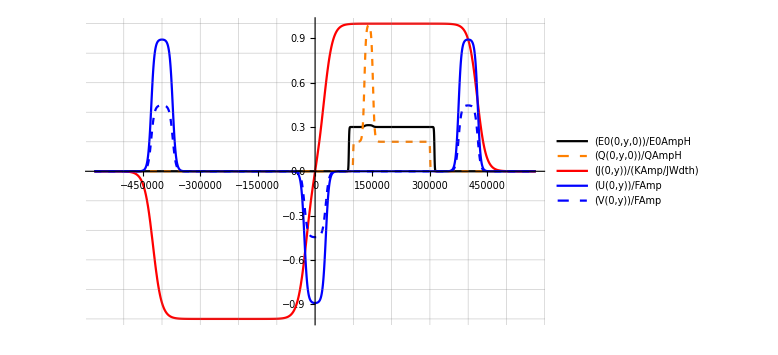

```mathematica
Plot[{
E0[0,y,0]/E0AmpH
,Q[0,y,0]/QAmpH
,J[0,y]/(KAmp/JWdth)
,U[0,y]/FAmp
,V[0,y]/FAmp
}
,{y,Min[x3],Max[x3]}
,PlotRange->All
,ImageSize->Large
,PlotStyle->{Black,{Orange,Dashed},Red,Blue,{Blue,Dashed}}
,PlotLegends->"Expressions"
,GridLines->All
]
```

```mathematica
l=6;
h=9;
bckgE=1500;(*eV*)
bckgQ=0.3;(*mW m^-2 or erg s^-1 cm^-2*)
ϕ[Ep_,x_,y_]:=Log10[(Max[Q[x,y,0],bckgQ]keVPerg)/(2(Max[E0[x,y,0],bckgE]keVPeV)^3)(10^Ep keVPeV)^2]-1/Log[10] 10^Ep/Max[E0[x,y,0],bckgE](*http://dx.doi.org/10.1029/2010GL045406*)
plotd=DensityPlot[
ϕ[e,0,y]
(*,{y,Min[x3],Max[x3]}*)
,{y,0,300000}
,{e,1,5}
,PlotRange->{l,h}
,PlotLegends->BarLegend[{Automatic,{l,h}},LegendLabel->"Log Differential Energy Flux [keV keV^-1 s^-1 cm^-2]"]
,ColorFunctionScaling->False
,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{l,h}]]&)
,PlotPoints->100
,ImageSize->Large
,AspectRatio->1/4
,FrameLabel->{"North [m]","log e^- energy [eV]"}
,GridLines->{None,{Log10[E0AmpL],Log10[E0AmpH]}}
];
plotb=Plot[{
Log10[(Max[Q[0,y,0],bckgQ]keVPerg)/(Max[E0[0,y,0],bckgE]keVPeV)]
}
,{y,0,300000}
,PlotRange->All
,ImageSize->Large
,PlotStyle->{Black,{Orange,Dashed},Red,Blue,{Blue,Dashed}}
,PlotLegends->"Expressions"
,Frame->True
,FrameLabel->{"North [m]","Log e^- flux [s^-1 cm^-2]"}
,AspectRatio->1/4
];
plotc=Plot[{
Max[Q[0,y,0],bckgQ]
}
,{y,0,300000}
,PlotRange->All
,ImageSize->Large
,PlotStyle->{Black,{Orange,Dashed},Red,Blue,{Blue,Dashed}}
,PlotLegends->"Expressions"
,Frame->True
,FrameLabel->{"North [m]","e^- energy flux [erg s^-1 cm^-2]"}
,AspectRatio->1/4
];
GraphicsColumn[{plotb,plotc,plotd}]
```

-Graphics-

```mathematica
P={
{1.24616,1.45903,-2.42269 10^-1,5.95459 10^-2}
,{2.23976,-4.22918 10^-7,1.36458 10^-2,2.53332 10^-3}
,{1.41754,1.44597 10^-1,1.70433 10^-2,6.39717 10^-4}
,{2.48775 10^-1,-1.50890 10^-1,6.30894 10^-9,1.23707 10^-3}
,{-4.65119 10^-1,-1.05081 10^-1,-8.95701 10^-2,1.22450 10^-2}
,{3.86019 10^-1,1.75430 10^-3,-7.42960 10^-4,4.60881 10^-4}
,{-6.45454 10^-1,8.49555 10^-4,-4.28581 10^-2,-2.99302 10^-3}
,{9.48930 10^-1,1.97385 10^-1,-2.50660 10^-3,-2.06938 10^-3}
};
```

```mathematica
H=(100kB Tn)/((m/10^3)g)
```

(100000 kB Tn)/(g m)

```mathematica
c[i_,E0_]:=Sum[P[[i,j+1]](Log[E0])^j,{j,0,3}]
f[y_,E0_]:=c[1,E0] y^C[2,E0] Exp[-c[3,E0] y^C[4,E0]]+C[5,E0] y^C[6,E0] Exp[-c[7,E0] y^c[8,E0]]
```

```mathematica
Import["D:\\Files\\Research\\AuroralML\\CDFs_Bond\\SW_EXPT_EFIA_TCT02_20160302T000000_20160302T034637_0302.cdf",{"Datasets","Timestamp"}]
```

{{2016,3,2,0,0,0.225},{2016,3,2,0,0,0.725},{2016,3,2,0,0,1.225},{2016,3,2,0,0,1.725},{2016,3,2,0,0,2.225},{2016,3,2,0,0,2.725},{2016,3,2,0,0,3.225},27176,{2016,3,2,3,46,35.225},{2016,3,2,3,46,35.725},{2016,3,2,3,46,36.225},{2016,3,2,3,46,36.725},{2016,3,2,3,46,37.225},{2016,3,2,3,46,37.725}}
 |  |  |  |